## Fig E

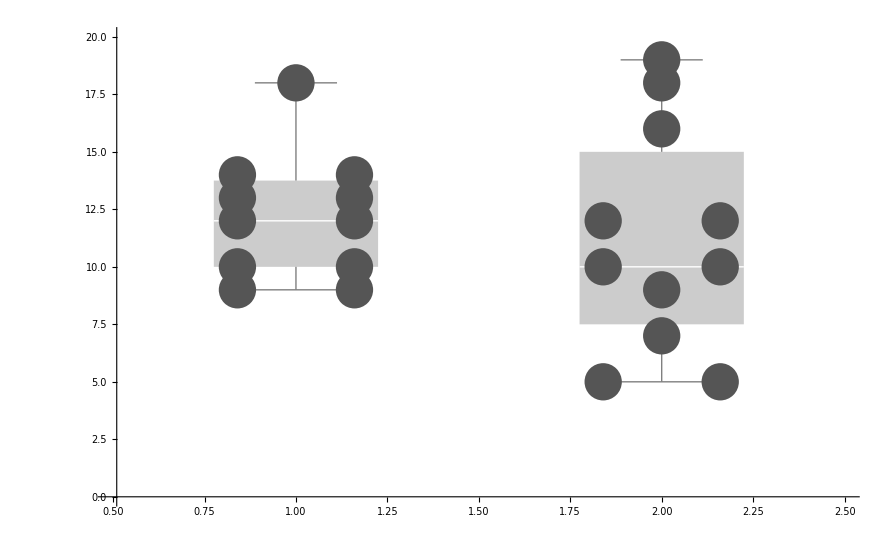

```mathematica
SetDirectory[NotebookDirectory[]];
c1=RGBColor[0.8,0.8,0.8];
c2=RGBColor[85/255,85/255,85/255];
clones={};
singles={};

Do[
s=Import["chambers//s"<>ToString[ii]<>".dat","List"];
AppendTo[clones,Length[DeleteCases[s,1]]];
AppendTo[singles,Length[s]-Length[DeleteCases[s,1]]];
,{ii,1,11}]
dxList[inList_,nn_,dx_]:=(
outList={};
usedList={};
inSort=Sort[inList];

Do[
If[Count[inSort,inSort[[ii]]]==1,
AppendTo[outList,{nn,inSort[[ii]]}],

If[Count[usedList,inSort[[ii]]]==0,
AppendTo[outList,{nn-dx,inSort[[ii]]}];
AppendTo[usedList,inSort[[ii]]],
AppendTo[outList,{nn+dx,inSort[[ii]]}]

]

];
If[Count[inSort,inSort[[ii]]]>2,Print["Repeats 3 times"]];

,{ii,1,Length[inSort]}];
outList)
c1=RGBColor[0.8,0.8,0.8];
c2=RGBColor[85/255,85/255,85/255];
dx=0.16;
bPR=ListPlot[{{10000,10000}},PlotRange->{{0.5,2.5},{0,20}}];
b0=BoxWhiskerChart[{clones,singles},PlotRange->{{0.5,2.5},{0,20}},ChartStyle->c1];
b1=ListPlot[{
dxList[singles,2,dx],
dxList[clones,1,dx]
},
PlotStyle->{{c2,PointSize->0.03}},PlotRange->{{0.5,2.5},{0,20}},Frame->True];
fige=Show[{bPR,b0,b1},PlotRange->{{0.5,2.5},{0,20}}]
```

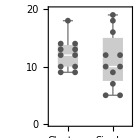

```mathematica
FigE=plotWhiskers[
{fige},
xTicks->{1,2},
yTicks->{0,5,10,15,20},
xReplace->{"Clusters","Singles"},
tickLength->0.12,
plotRange->{{0.6,2.4},{0,20}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.05,0.2,1,0.3},
plotLabels->{
Row[{}],
Row[{Style["Number per chamber"]}]},
labelsDistance->{0.8,0.65},
plotTitle->True,
titleText->"",
titleDistance->0.3,
fontMain->7,
fontName->"Helvetica"
]
```

## Fig F

```mathematica
points={};
Do[
c=Import["chambers//c"<>ToString[i]<>".dat","List"];
AppendTo[points,{Total[c],Length[c]}];
,{i,1,21}];
Do[
c=Import["chambers//s"<>ToString[i]<>".dat","List"];
AppendTo[points,{Total[c],Length[c]}];
,{i,1,11}];

lm=LinearModelFit[Sort[points],x2,x2];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 21.9964 | 1.11473 | 19.7324 | 9.83378×10^-19
x2 | 0.0255056 | 0.0025958 | 9.82572 | 6.87937×10^-11

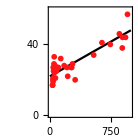

```mathematica
figf1=ListPlot[points,PlotStyle->{RGBColor[255/255,21/255,21/255],PointSize->0.03},PlotRange->{{0,1000},{0,60}},Frame->True];
figf2=Plot[22+0.026*x2,{x2,0,1000},PlotRange->{{0,1000},{0,60}},PlotStyle->Black];
figf=Show[figf2,figf1];
figF=plot[
{figf},
xTicks->{0,250,500,750,1000},
yTicks->{0,20,40,60},
tickLength->0.12,
plotRange->{{0,1000},{0,60}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.05,0.2,1,0.3},
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Cluster number"]}]},
labelsDistance->{0.5,0.65},
plotTitle->True,
titleText->"",
titleDistance->0.3,
fontMain->7,
fontName->"Helvetica"
];
t=Text[Row[{Style["~",FontFamily->"Helvetica",FontSize->7],Subscript[Style["p",Italic,FontFamily->"Helvetica",FontSize->7],Style["c",FontSize->5,FontFamily->"Helvetica"]],Style[" = 0.026",FontFamily->"Helvetica",FontSize->7]}]];
FigF=figure[
5,
5,
elements->{figF,t},
elementCoordinates->{{0,0},{2.5,-1.8}},
fontSize->10]
```

## Figure

```mathematica
stage1=Text[Row[{Style["‘stage 1’",FontFamily->"Helvetica",FontSize->7]}]];
FigED1=figure[
5,
9.2,
elements->{FigE,FigF,stage1},
elementCoordinates->{{0,0},{0,-4.7},{0+1+3*6/5/2,-0.5}},
fontSize->10,
centeredElements->{3}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figs//SYS_ED_fig1.pdf",FigED1]
```

figs//SYS_ED_fig1.pdf